```mathematica
Table[LegendreP[n,z],{n,0,5}]
```

{1,z,1/2 (-1+3 z^2),1/2 (-3 z+5 z^3),1/8 (3-30 z^2+35 z^4),1/8 (15 z-70 z^3+63 z^5)}

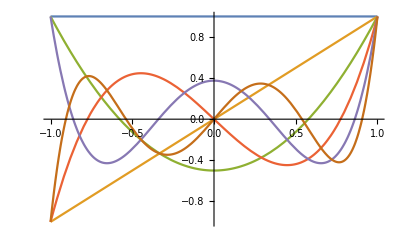

```mathematica
Plot[%,{z,-1,1}]
```

```mathematica
Table[Integrate[LegendreP[n,z]*LegendreP[n,z],{z,-1,1}],{n,0,5}]
```

{2,2/3,2/5,2/7,2/9,2/11}

```mathematica
Table[LegendreP[n,Cos[θ]],{n,0,5}]
```

{1,Cos[θ],1/2 (-1+3 Cos[θ]^2),1/2 (-3 Cos[θ]+5 Cos[θ]^3),1/8 (3-30 Cos[θ]^2+35 Cos[θ]^4),1/8 (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)}

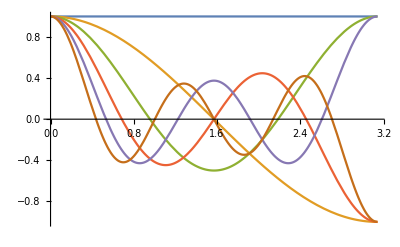

```mathematica
Plot[%,{θ,0,π}]
```

```mathematica
Table[LegendreP[l,m,Cos[θ]],{l,0,5},{m,-l,l}]//Simplify
```

{{1},{1/2 √(Sin[θ]^2),Cos[θ],-√(Sin[θ]^2)},{Sin[θ]^2/8,1/2 Cos[θ] √(Sin[θ]^2),1/4 (1+3 Cos[2 θ]),-3 Cos[θ] √(Sin[θ]^2),3 Sin[θ]^2},{1/48 (Sin[θ]^2)^(3/2),1/8 Cos[θ] Sin[θ]^2,1/8 (-1+5 Cos[θ]^2) √(Sin[θ]^2),1/8 (3 Cos[θ]+5 Cos[3 θ]),-3/2 (-1+5 Cos[θ]^2) √(Sin[θ]^2),15 Cos[θ] Sin[θ]^2,-15 (Sin[θ]^2)^(3/2)},{Sin[θ]^4/384,1/48 Cos[θ] (Sin[θ]^2)^(3/2),1/96 (5+7 Cos[2 θ]) Sin[θ]^2,1/8 Cos[θ] (-3+7 Cos[θ]^2) √(Sin[θ]^2),1/64 (9+20 Cos[2 θ]+35 Cos[4 θ]),-5/2 Cos[θ] (-3+7 Cos[θ]^2) √(Sin[θ]^2),15/4 (5+7 Cos[2 θ]) Sin[θ]^2,-105 Cos[θ] (Sin[θ]^2)^(3/2),105 Sin[θ]^4},{((Sin[θ]^2)^(5/2))/3840,1/384 Cos[θ] Sin[θ]^4,1/384 (-1+9 Cos[θ]^2) (Sin[θ]^2)^(3/2),1/64 (5 Cos[θ]+3 Cos[3 θ]) Sin[θ]^2,1/16 (1-14 Cos[θ]^2+21 Cos[θ]^4) √(Sin[θ]^2),1/8 Cos[θ] (15-70 Cos[θ]^2+63 Cos[θ]^4),-15/8 (1-14 Cos[θ]^2+21 Cos[θ]^4) √(Sin[θ]^2),105/8 (5 Cos[θ]+3 Cos[3 θ]) Sin[θ]^2,-105/2 (-1+9 Cos[θ]^2) (Sin[θ]^2)^(3/2),945 Cos[θ] Sin[θ]^4,-945 (Sin[θ]^2)^(5/2)}}

```mathematica
Table[{l,m,SphericalHarmonicY[l,m,θ,ϕ]},{l,0,5},{m,-l,l}]
```

{{{0,0,1/(2 √π)}},{{1,-1,1/2 ⅇ^(-ⅈ ϕ) √(3/(2 π)) Sin[θ]},{1,0,1/2 √(3/π) Cos[θ]},{1,1,-1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ]}},{{2,-2,1/4 ⅇ^(-2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2},{2,-1,1/2 ⅇ^(-ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ]},{2,0,1/4 √(5/π) (-1+3 Cos[θ]^2)},{2,1,-1/2 ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ]},{2,2,1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2}},{{3,-3,1/8 ⅇ^(-3 ⅈ ϕ) √(35/π) Sin[θ]^3},{3,-2,1/4 ⅇ^(-2 ⅈ ϕ) √(105/(2 π)) Cos[θ] Sin[θ]^2},{3,-1,1/8 ⅇ^(-ⅈ ϕ) √(21/π) (-1+5 Cos[θ]^2) Sin[θ]},{3,0,1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3)},{3,1,-1/8 ⅇ^(ⅈ ϕ) √(21/π) (-1+5 Cos[θ]^2) Sin[θ]},{3,2,1/4 ⅇ^(2 ⅈ ϕ) √(105/(2 π)) Cos[θ] Sin[θ]^2},{3,3,-1/8 ⅇ^(3 ⅈ ϕ) √(35/π) Sin[θ]^3}},{{4,-4,3/16 ⅇ^(-4 ⅈ ϕ) √(35/(2 π)) Sin[θ]^4},{4,-3,3/8 ⅇ^(-3 ⅈ ϕ) √(35/π) Cos[θ] Sin[θ]^3},{4,-2,3/8 ⅇ^(-2 ⅈ ϕ) √(5/(2 π)) (-1+7 Cos[θ]^2) Sin[θ]^2},{4,-1,3/8 ⅇ^(-ⅈ ϕ) √(5/π) Cos[θ] (-3+7 Cos[θ]^2) Sin[θ]},{4,0,(3 (3-30 Cos[θ]^2+35 Cos[θ]^4))/(16 √π)},{4,1,-3/8 ⅇ^(ⅈ ϕ) √(5/π) Cos[θ] (-3+7 Cos[θ]^2) Sin[θ]},{4,2,3/8 ⅇ^(2 ⅈ ϕ) √(5/(2 π)) (-1+7 Cos[θ]^2) Sin[θ]^2},{4,3,-3/8 ⅇ^(3 ⅈ ϕ) √(35/π) Cos[θ] Sin[θ]^3},{4,4,3/16 ⅇ^(4 ⅈ ϕ) √(35/(2 π)) Sin[θ]^4}},{{5,-5,3/32 ⅇ^(-5 ⅈ ϕ) √(77/π) Sin[θ]^5},{5,-4,3/16 ⅇ^(-4 ⅈ ϕ) √(385/(2 π)) Cos[θ] Sin[θ]^4},{5,-3,1/32 ⅇ^(-3 ⅈ ϕ) √(385/π) (-1+9 Cos[θ]^2) Sin[θ]^3},{5,-2,1/8 ⅇ^(-2 ⅈ ϕ) √(1155/(2 π)) Cos[θ] (-1+3 Cos[θ]^2) Sin[θ]^2},{5,-1,1/16 ⅇ^(-ⅈ ϕ) √(165/(2 π)) (1-14 Cos[θ]^2+21 Cos[θ]^4) Sin[θ]},{5,0,1/16 √(11/π) (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)},{5,1,-1/16 ⅇ^(ⅈ ϕ) √(165/(2 π)) (1-14 Cos[θ]^2+21 Cos[θ]^4) Sin[θ]},{5,2,1/8 ⅇ^(2 ⅈ ϕ) √(1155/(2 π)) Cos[θ] (-1+3 Cos[θ]^2) Sin[θ]^2},{5,3,-1/32 ⅇ^(3 ⅈ ϕ) √(385/π) (-1+9 Cos[θ]^2) Sin[θ]^3},{5,4,3/16 ⅇ^(4 ⅈ ϕ) √(385/(2 π)) Cos[θ] Sin[θ]^4},{5,5,-3/32 ⅇ^(5 ⅈ ϕ) √(77/π) Sin[θ]^5}}}

```mathematica
Table[SphericalPlot3D[Abs[SphericalHarmonicY[l,m,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->All,PlotLabel->{l,m}],{l,0,3},{m,-l,l}]
```

{{-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}